Create a CAMB input file for the Planck13 LCDM cosmology:

```mathematica
Needs["DeepZot`CosmoTools`"]
```

```mathematica
cLight=Convert[SpeedOfLight,Kilo Meter/Second]/(Kilo Meter/Second);
```

```mathematica
createCosmology[Planck13]
```

```mathematica
SetDirectory["/Users/david/Cosmo/DESC/DarkEnergySchool/LargeScaleStructureStatistics/camb/"];
```

```mathematica
exportToCamb["Planck13.camb",Planck13,redshifts->{0,1.2},kmax->100]
```

Planck13.camb

```mathematica
Needs["DeepZot`PowerTools`"]
```

```mathematica
Planck13Data=ReadList["Planck13_matterpower_1.dat",Number,RecordLists->True];
```

```mathematica
Planck13Pk=makePower[Planck13Data];
```

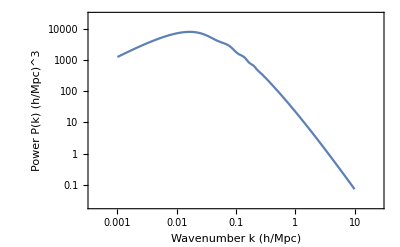

```mathematica
LogLogPlot[Planck13Pk[k],{k,0.001,10},GridLines->Automatic,Frame->True,FrameLabel->{"Wavenumber k (h/Mpc)","Power P(k) (h/Mpc)^3"}]
```

Compare the corresponding correlation functions:

```mathematica
{rmin,rmax,veps}={1,200,0.001};
Planck13Xi=sbTransform[Planck13Pk,rmin,rmax,0,veps];
```

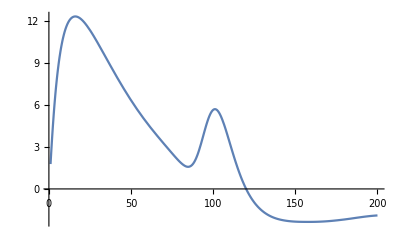

```mathematica
Plot[r^2Planck13Xi[r],{r,rmin,rmax}]
```

Calculate scale keq of matter-radiation equality:

```mathematica
Sqrt[2Ωmat[Planck13][0](H0[Planck13]/cLight)^2 3403]
```

0.0104082

Calculate the linear growth function:

```mathematica
Gz=growthFunction[Planck13,5];
```

Calculate scale where total variance of fluctuations from 0.01 < k < kNL (in h/Mpc) reaches 0.1 or 1, as an indicator of the onset of non-linear growth:

```mathematica
Pkz0=makePower[ReadList["Planck13_matterpower_2.dat",Number,RecordLists->True]];
```

```mathematica
kVariance=growthVarianceFunction[Pkz0,0.01,10,inverted->True];
```

```mathematica
nlData=With[{z0=1.2},
Module[{z,kNLlo,kNLhi},
Table[
kNLlo=kVariance[0.1/Gz[z]];
kNLhi=kVariance[1.0/Gz[z]];
{
z,kNLlo,kNLhi
},
{z,Range[0.,5.,0.1]}
]
]
];
```

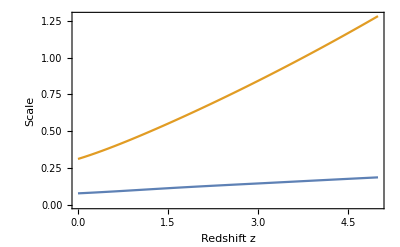

```mathematica
ListPlot[{nlData[[;;,{1,2}]],nlData[[;;,{1,3}]]},Joined->True,Frame->True,FrameLabel->{"Redshift z","Scale"}]
```

```mathematica
Export["nonlinearity.dat",nlData];
```